```mathematica
(*Tyrone Bamfo and Alexander Scotte*)
sigma = 3.8*10^-19;
nSap=1.76;
tau=3.2*10^-6;
lambda=8*10^-5;
lambdapump=5.32*10^-5;
c=2.9925458*10^10;
nupump=c/lambdapump;
h=6.626*10^-34;
nu0=c/lambda;
```

```mathematica
iSat=h nu0/(sigma tau)
```

203830.

```mathematica
length=1;
loss = 0.017
gain = 25*loss
Trans = Sqrt[gain*loss]-loss
R1 = 1- loss
R2 = 1 - Trans
nthreshold=1/(2 sigma length)Log[1/(R1*R2)]
```

0.017

0.425

0.068

0.983

0.932

1.15222×10^17

```mathematica
inversion =Table[nthreshold*i, {i, 1.001, 5.001}]
```

{1.15337×10^17,2.30559×10^17,3.45781×10^17,4.61003×10^17,5.76225×10^17}

```mathematica
intensityOut=iSat/2*0.08*(inversion/nthreshold-1)
```

{8.15321,8161.36,16314.6,24467.8,32621.}

```mathematica
beamArea=1/intensityOut (*1W divided by output intensity yields necessary spot size*)
```

{0.122651,0.000122529,0.0000612949,0.0000408701,0.0000306551}

```mathematica
omega0=Sqrt[2beamArea/Pi]*10^4 (*in microns*)
```

{2794.32,88.3199,62.4672,51.0085,44.1765}

```mathematica
z0=nSap Pi (omega0^2 *10^-8)/lambda (*see if spot sizes are
                                    (physically reasonable*)
```

{5396.65,5.39126,2.69698,1.79828,1.34882}

```mathematica
totalN=beamArea*length*inversion
```

{1.62397×10^16,3.24307×10^13,2.43312×10^13,2.16295×10^13,2.02783×10^13}

```mathematica
pumpPower=(totalN/tau)h nupump (1/1.0)
```

{1647.67,3.29041,2.46863,2.19452,2.05743}

{{0.+1. (1. (1.+1/5 (-0.284091-1. l))+1/5 (-0.284091-40 (1.+1/5 (-0.284091-1. l))-1. l)),1/2 (1. (1.+1/5 (-0.284091-1. l))+1/5 (-0.284091-40 (1.+1/5 (-0.284091-1. l))-1. l))+1.76 (0.284091+40 (1.+1/5 (-0.284091-1. l))+1. l+(1. (1.+1/5 (-0.284091-1. l))+1/5 (-0.284091-40 (1.+1/5 (-0.284091-1. l))-1. l)) l)},{0.681818,0.340909+1.76 (-3.97727+0.681818 l)}}

6.38258

4.71591

5.54924

0.00460659

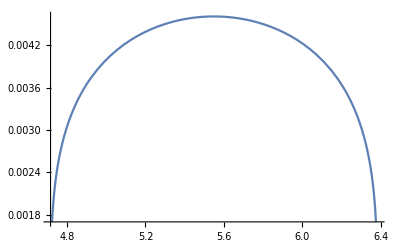

```mathematica
Clear[l, lcol]
lcol=20; (*length of collimated arm of the cavity*)
n=1.76;
m1={{1.0,0}, {-2/10,1}}; (*10cm radius of curvature*)
lxtal={{1.0, length/2}, {0,1}};
exit={{1,0},{0,n}}; (*abcd for leaving dielectric*)
enter={{1,0}, {0,1/n}}; (*abcd for entering dielectric*)
l1={{1,l},{0,1}}; (*plot in terms of length l, distance between curved mirror and xtal*)
l2={{1,lcol},{0,1}};
abcd=lxtal.enter.l1.m1.l2.l2.m1.l1.exit.lxtal
a1=Simplify[abcd[[1,1]]];
b1=Simplify[abcd[[1,2]]];
c1=Simplify[abcd[[2,1]]];
d1=Simplify[abcd[[2,2]]];
lmax=NSolve[ (a1+d1)/2==1,l][[1,1,2]]
lmin=NSolve[ (a1+d1)/2==-1,l][[1,1,2]]
omega=Sqrt[(lambda/n/Pi)Abs[b1]/Sqrt[1-a1^2]];
l = (lmax-lmin)/2 + lmin
Print[omega]
Plot[omega, {l,lmin, lmax}]
```

5.54924

0.+1.87433 ⅈ

(2.27333+0.0937163 ⅈ)/((0.+1.87433 ⅈ) (0.+1. (1.02+0.05 l4))+1/2 (1.02+0.05 l4)+1.76 (5.54924 (1.02+0.05 l4)+1. (0.4+1. l4)))

1/Re[(2.27333+0.0937163 ⅈ)/((0.+1.87433 ⅈ) (0.+1. (1.02+0.05 l4))+1/2 (1.02+0.05 l4)+1.76 (5.54924 (1.02+0.05 l4)+1. (0.4+1. l4)))]

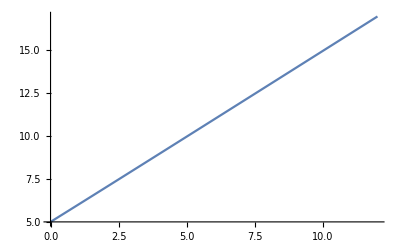

0.0041151 √(-1/Im[(2.27333+0.0937163 ⅈ)/((0.+1.87433 ⅈ) (0.+1. (1.02+0.05 l4))+1/2 (1.02+0.05 l4)+1.76 (5.54924 (1.02+0.05 l4)+1. (0.4+1. l4)))])

15.5

0.105433

20.4623

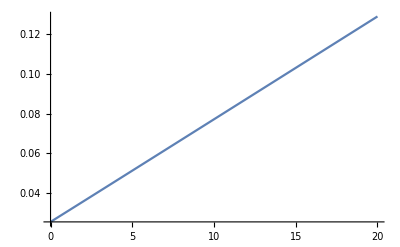

```mathematica
n=1.5;
curve={{1.,0}, {(1.-1/n)/10.,1/n}}//N; (*enter curved dielectric*)
t={{1,0.6},{0,1}}; (*propagate 0.6 cm*)
n3={{1.,0},{0,n}}; (*leave dielectric*)
lens=n3.t.curve//N;
travel = (lmax-lmin)/2 + lmin
distance={{1,travel},{0,1.}}; (*center of stability range*)
focuslength={{1,l4},{0,1}};

abcd2=focuslength.lens.distance.exit.lxtal;
omegapump = 0.0046; (*spot size in crystal*)
lamdapump=5.32*10^(-5);
q=I n Pi omegapump^2 / lamdapump (*q of pump in crystal*)

a2=abcd2[[1,1]];
b2=abcd2[[1,2]];
c2=abcd2[[2,1]];
d2=abcd2[[2,2]];
q2= (a2 q + b2)/(c2 q + d2);
qinv = 1/q2
curvature = 1/Re[qinv]
Plot[curvature, {l4,0,12}] (*radius of curvature of beam*)
beamSize =Sqrt[-lamdapump/Pi/Im[qinv]]
l4 = 15.5
Print[beamSize]
Print[curvature]
Clear[l4]
Plot[beamSize, {l4,0,20}] (*beam size*)
```

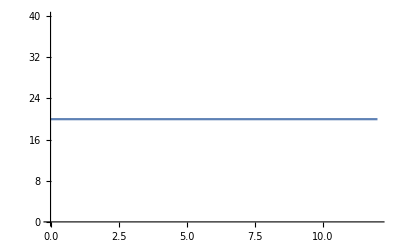

-Graphics-

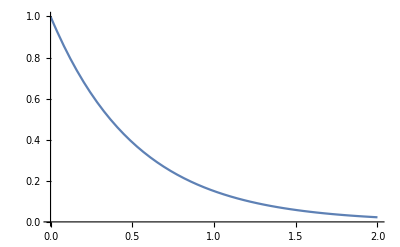

```mathematica
sigmaAbs=2.2*10^-20;
No=8.623*10^19;
Plot[Exp[-sigmaAbs No z], {z,0,2}]
```

```mathematica
(*data found during the calculation that will be used
omega0 = 44.17651501552232
z0 = 1.348824538593708
totalN = 1.7664224077779906*^13
pump power = 2.057430587281344 W
range cavity (distance from crystal)= 6.186497326203209 - 4.715909090909091 cm
center 5.45120320855615cm with spotsize 0.004606588659617788cm
position pump lense(using data pumplaser pump = 0.010554): around 15.5cm(from graph)
lense radius: around 20.4 cm(from graph)
*)
```